```mathematica
ClearAll[]

fact = 178.9818;
time=0.045;
dim=16;

Γ=Import["C:\\Users\\aless\\OneDrive - Università degli Studi di Parma\\Documents\\Lavoro\\QEC_FT\\optimization_codewords\\Gamma_08apr.txt","Table"]*fact;
γ=Array[0,{dim,dim}];
Do[γ[[m,n]]=2*Γ[[m,n]]-Γ[[m,m]]-Γ[[n,n]],{m,dim},{n,dim}];
γ=(γ+Transpose[γ])/2;

χ=Exp[γ*time];
{eigs,vecs}=Eigensystem[χ];
(* vecs[[1]]=-vecs[[1]];
vecs[[4]]=-vecs[[4]];*)

Pr=ConstantArray[0,{dim,dim}];
Do[Pr[[k,k]]=1,{k,dim}];

(* Error operators *)
Er =ConstantArray[0,{dim,dim}];
Do[Do[Er[[j,k]]=Er[[j,k]]+Sqrt[eigs[[k]]]*vecs[[k,m]]*Pr[[j,m]],{j,dim},{m,dim}],{k,dim}]
```

```mathematica
(*Er[[All,2]]=-Er[[All,2]];*)
MatrixForm[Er]
```

(-0.962976 | 0.267581 | -0.0327303 | -0.00238674 | 0.000128494 | 0.-8.81157×10^-6 ⅈ | 0.+0.0000112551 ⅈ | -4.19464×10^-6 | 8.94518×10^-6 | 5.70307×10^-6 | 0.-6.65773×10^-6 ⅈ | 1.12796×10^-6 | 0.-4.32726×10^-7 ⅈ | 0.+1.89859×10^-6 ⅈ | 1.22391×10^-6 | -4.33113×10^-7
-0.963016 | -0.267446 | -0.0326658 | 0.00238074 | 0.000128357 | 0.-0.0000115733 ⅈ | 0.+5.88943×10^-6 ⅈ | 6.48745×10^-7 | 7.41064×10^-7 | 7.04401×10^-7 | 0.+9.97192×10^-6 ⅈ | -7.09266×10^-8 | 0.-7.97093×10^-7 ⅈ | 0.-3.18721×10^-6 ⅈ | -1.35881×10^-6 | 1.21324×10^-6
-0.998911 | 0.0424517 | 0.0193381 | 0.000927232 | 0.000100076 | 0.-1.44245×10^-6 ⅈ | 0.-8.87771×10^-7 ⅈ | -2.71945×10^-6 | 7.09064×10^-8 | -2.80639×10^-6 | 0.+4.53809×10^-6 ⅈ | -2.13835×10^-6 | 0.+1.72876×10^-6 ⅈ | 0.-1.43485×10^-6 ⅈ | 1.13017×10^-6 | -5.49153×10^-6
-0.998924 | -0.042133 | 0.0193585 | -0.00092417 | 0.000100176 | 0.+3.2096×10^-6 ⅈ | 0.-9.97825×10^-7 ⅈ | -5.20081×10^-6 | -4.53236×10^-6 | -9.38265×10^-7 | 0.+8.85467×10^-7 ⅈ | 4.26842×10^-6 | 0.-4.50733×10^-7 ⅈ | 0.+4.81047×10^-6 ⅈ | -8.17945×10^-6 | 3.71419×10^-7
-0.967468 | 0.251615 | -0.0263305 | -0.00126021 | 2.6045×10^-6 | 0.+0.0000217482 ⅈ | 0.-8.9198×10^-6 ⅈ | 4.75985×10^-6 | -9.82089×10^-6 | -6.45948×10^-6 | 0.+8.36578×10^-6 ⅈ | -5.75881×10^-6 | 0.+1.84111×10^-6 ⅈ | 0.-1.63402×10^-6 ⅈ | -5.0165×10^-7 | 6.8467×10^-7
-0.967449 | -0.251687 | -0.0263508 | 0.00126828 | 2.43277×10^-6 | 0.+0.0000129155 ⅈ | 0.-0.0000101597 ⅈ | 6.70485×10^-6 | -6.15463×10^-7 | -6.4237×10^-6 | 0.-0.0000149845 ⅈ | 2.65585×10^-6 | 0.-2.99722×10^-7 ⅈ | 0.+2.46047×10^-6 ⅈ | 9.14186×10^-7 | -1.14004×10^-6
-0.99713 | 0.0738214 | 0.0167114 | 0.00150308 | 0.0000485922 | 0.+0.000014124 ⅈ | 0.-0.0000120396 ⅈ | -3.35035×10^-6 | 0.0000114751 | 0.0000144418 | 0.-1.57987×10^-6 ⅈ | 4.63555×10^-6 | 0.+4.11237×10^-6 ⅈ | 0.-2.64049×10^-6 ⅈ | 5.85129×10^-7 | 1.54849×10^-6
-0.997127 | -0.07386 | 0.0167091 | -0.0015067 | 0.0000484478 | 0.-2.48884×10^-6 ⅈ | 0.-1.58798×10^-6 ⅈ | 6.00474×10^-7 | -2.3175×10^-6 | -9.23758×10^-6 | 0.+6.98722×10^-6 ⅈ | 0.0000119095 | 0.-1.09604×10^-7 ⅈ | 0.+2.13713×10^-6 ⅈ | 5.97468×10^-6 | 1.41009×10^-6
-0.996474 | 0.0823949 | 0.0157445 | 0.00163228 | 0.0000299806 | 0.-4.97057×10^-6 ⅈ | 0.-8.71932×10^-6 ⅈ | 7.97663×10^-7 | 4.94564×10^-6 | -3.7783×10^-8 | 0.+1.33992×10^-6 ⅈ | -0.0000129593 | 0.-5.56782×10^-6 ⅈ | 0.+4.71521×10^-6 ⅈ | 2.22366×10^-6 | 1.33131×10^-6
-0.996463 | -0.0825324 | 0.0157302 | -0.00163708 | 0.0000281152 | 0.+1.98155×10^-6 ⅈ | 0.+8.58396×10^-7 ⅈ | -0.0000114521 | -0.0000100948 | 1.51832×10^-6 | 0.-8.33138×10^-6 ⅈ | -2.17319×10^-6 | 0.-5.73746×10^-6 ⅈ | 0.-6.75552×10^-6 ⅈ | 4.84063×10^-7 | 5.63123×10^-7
-0.994366 | 0.105227 | 0.0126432 | 0.00189773 | -0.0000210197 | 0.+9.93539×10^-7 ⅈ | 0.+0.0000204937 ⅈ | 0.0000155699 | -0.0000156985 | 7.38596×10^-6 | 0.-3.95784×10^-6 ⅈ | 3.07174×10^-7 | 0.+1.88949×10^-6 ⅈ | 0.+1.22224×10^-6 ⅈ | 1.09006×10^-6 | 5.2915×10^-7
-0.994369 | -0.105202 | 0.0126497 | -0.00189997 | -0.0000221905 | 0.-0.0000199682 ⅈ | 0.-4.68174×10^-6 ⅈ | 0.0000106307 | 3.74129×10^-6 | -6.12693×10^-6 | 0.-4.96248×10^-6 ⅈ | -7.45433×10^-6 | 0.+6.76078×10^-6 ⅈ | 0.-1.90031×10^-6 ⅈ | -1.05502×10^-6 | 1.03686×10^-6
-0.977834 | 0.209068 | -0.0114432 | 0.000825551 | -0.00016098 | 0.-0.0000215927 ⅈ | 0.-0.0000159651 ⅈ | 3.15058×10^-6 | -4.78071×10^-6 | 3.38434×10^-6 | 0.+8.16278×10^-7 ⅈ | 7.92517×10^-6 | 0.-2.59448×10^-6 ⅈ | 0.-9.05888×10^-7 ⅈ | -1.61038×10^-6 | -8.00907×10^-7
-0.977806 | -0.209196 | -0.0114775 | -0.000819635 | -0.000159674 | 0.+3.36662×10^-7 ⅈ | 0.+2.44081×10^-6 ⅈ | -0.0000207804 | -5.27693×10^-6 | 9.06319×10^-6 | 0.+3.87634×10^-6 ⅈ | -4.11337×10^-6 | 0.+3.30556×10^-6 ⅈ | 0.+3.34504×10^-6 ⅈ | 1.57853×10^-6 | -4.83578×10^-7
-0.988457 | 0.151433 | 0.00398686 | 0.00197317 | -0.000127213 | 0.+4.35142×10^-6 ⅈ | 0.+0.0000148368 ⅈ | -0.0000126424 | 0.0000103225 | -0.0000153285 | 0.-2.15966×10^-6 ⅈ | 1.44506×10^-6 | 0.+4.57392×10^-7 ⅈ | 0.-1.39284×10^-6 ⅈ | -1.35283×10^-6 | 7.42099×10^-7
-0.988441 | -0.15154 | 0.00396723 | -0.00197356 | -0.000126111 | 0.+0.0000111869 ⅈ | 0.+8.18457×10^-6 ⅈ | 0.0000174773 | 0.0000128954 | 5.15757×10^-6 | 0.+5.85244×10^-6 ⅈ | 3.93593×10^-7 | 0.-4.10582×10^-6 ⅈ | 0.-7.3804×10^-7 ⅈ | -1.14625×10^-6 | -1.08129×10^-6)

```mathematica
acc=0;
Do[acc=acc+Er[[k,j]]*Er[[k,j]],{k,dim},{j,dim/2}]
1-acc/dim
```

1.01489×10^-10+0. ⅈ

```mathematica
b=ConstantArray[0,{dim}];
Do[b[[k]]=1,{k,dim-1,dim}];
B=ConstantArray[0,{dim,dim}];
A=ConstantArray[0,{38,dim}];
z=ConstantArray[0,dim];
zL=ConstantArray[0,{dim}];
oL=ConstantArray[0,{dim}];
ew0=ConstantArray[0,{dim/2,dim}];
ew1=ConstantArray[0,{dim/2,dim}];
inds={1,2,9,3,10,4,16,11,5,15,12,6,7,8};
(*inds=RandomSample[Range[23],dim-2];*)
```

```mathematica
(* code words*)
x =1;
While[x>1/1000000,
zero=Sort[Join[RandomSample[{15,7,5,13,9,1,3,11},4],RandomSample[{12,4,16,2,10,8,14,6},4]]];
(*zero=Sort[RandomSample[Range[16],8]];*)
(* zero ={2,4,5,7,9,12}; *)
uno=Complement[Range[dim],zero];
cw=Flatten[{zero, uno}];
Do[z[[k]]=1,{k,dim/2+1,dim}];

Do[m=1; Do[Do[A[[m,j]]=Sqrt[eigs[[k]]*eigs[[l]]]*vecs[[l,cw[[j]]]]*vecs[[k,cw[[j]]]]*(-1)^z[[j]];m=m+1,{l,k,dim/2}],{k,1,dim/2}],{j,1,dim}];

Do[B[[j,k]]=A[[inds[[j]],k]],{j,1,dim-2},{k,1,dim}];
Do[B[[dim-1,k]]=z[[k]],{k,1,dim}];
Do[B[[dim,k]]=1-z[[k]],{k,1,dim}];
x=Total[Abs[Im[Sqrt[PseudoInverse[B,Tolerance->0].b]]]]]

y=Sqrt[PseudoInverse[B,Tolerance->0].b] (* we can specify Tolerance --> 0 *)
Det[B]
```

{0.284136+3.86277×10^-14 ⅈ,0.187327-9.47026×10^-14 ⅈ,0.633965+5.15358×10^-14 ⅈ,0.484639-4.26345×10^-14 ⅈ,0.172796+6.90847×10^-14 ⅈ,0.317518-7.5779×10^-16 ⅈ,0.220267-1.42824×10^-14 ⅈ,0.26114-5.28288×10^-14 ⅈ,0.552343+1.10637×10^-13 ⅈ,0.383697+4.02533×10^-14 ⅈ,0.266209-1.00769×10^-13 ⅈ,0.120134-2.6335×10^-13 ⅈ,0.290425-1.4808×10^-13 ⅈ,0.49903+1.48705×10^-14 ⅈ,0.283788+7.31548×10^-14 ⅈ,0.220185-1.48368×10^-14 ⅈ}

-6.99007×10^-64+0. ⅈ

```mathematica
MatrixForm[y]
```

(0.284136+3.86277×10^-14 ⅈ
0.187327-9.47026×10^-14 ⅈ
0.633965+5.15358×10^-14 ⅈ
0.484639-4.26345×10^-14 ⅈ
0.172796+6.90847×10^-14 ⅈ
0.317518-7.5779×10^-16 ⅈ
0.220267-1.42824×10^-14 ⅈ
0.26114-5.28288×10^-14 ⅈ
0.552343+1.10637×10^-13 ⅈ
0.383697+4.02533×10^-14 ⅈ
0.266209-1.00769×10^-13 ⅈ
0.120134-2.6335×10^-13 ⅈ
0.290425-1.4808×10^-13 ⅈ
0.49903+1.48705×10^-14 ⅈ
0.283788+7.31548×10^-14 ⅈ
0.220185-1.48368×10^-14 ⅈ)

```mathematica
Max[Abs[PseudoInverse[B].B-IdentityMatrix[dim]]]
```

1.11759×10^-8

```mathematica
(* determine orthogonal set of error words *)
```

```mathematica
Do[zL[[zero[[k]]]]=Re[y[[k]]],{k,1,dim/2}];
Do[oL[[uno[[k]]]]=Re[y[[k+dim/2]]],{k,1,dim/2}];
Do[ew0[[j,k]]=Er[[k,j]]*zL[[k]],{k,1,dim},{j,1,dim/2}];
Do[ew1[[j,k]]=Er[[k,j]]*oL[[k]],{k,1,dim},{j,1,dim/2}];
Subscript[ψ, 0]=Transpose[Orthogonalize[ew0]]; (* we can specify other method than Gram Schmidt and tolerance *)
Subscript[ψ, 1]=Transpose[Orthogonalize[ew1]];  (* columns are orthogonal error words *)

(* Projectors & Correctors *)
Pp=ConstantArray[0,{dim,dim,dim/2}];
Cr=ConstantArray[0,{dim,dim,dim/2}];
Do[Pp[[j,k,l]]=Subscript[ψ, 0][[j,l]]*Conjugate[Subscript[ψ, 0][[k,l]]]+Subscript[ψ, 1][[j,l]]*Conjugate[Subscript[ψ, 1][[k,l]]],{j,1,dim},{k,1,dim},{l,1,dim/2}];

Do[Subscript[θ, 0]=-ArcCos[Conjugate[zL].Subscript[ψ, 0][[All,k]]]; 
Subscript[θ, 1]=-ArcCos[Conjugate[oL].Subscript[ψ, 1][[All,k]]]; 
Subscript[v, 0]=Normalize[Subscript[ψ, 0][[All,k]]-(Conjugate[zL].Subscript[ψ, 0][[All,k]])*zL];
Subscript[v, 1]=Normalize[Subscript[ψ, 1][[All,k]]-(Conjugate[oL].Subscript[ψ, 1][[All,k]])*oL];
Cr[[All,All,k]]=Cos[Subscript[θ, 0]]*(Outer[Times,zL,Conjugate[zL]]+Outer[Times,Subscript[v, 0],Conjugate[Subscript[v, 0]]])+Sin[Subscript[θ, 0]]*(-Outer[Times,zL,Conjugate[Subscript[v, 0]]]+ Outer[Times,Subscript[v, 0],Conjugate[zL]])+Cos[Subscript[θ, 1]]*(Outer[Times,oL,Conjugate[oL]]+Outer[Times,Subscript[v, 1],Conjugate[Subscript[v, 1]]])+Sin[Subscript[θ, 1]]*(-Outer[Times,oL,Conjugate[Subscript[v, 1]]]+ Outer[Times,Subscript[v, 1],Conjugate[oL]]),{k,1,dim/2}];
```

```mathematica
(* test ideal QEC *)
α=1/Sqrt[2];
β=1/Sqrt[2];
Subscript[ψ, i]=α*zL+β*oL;
ρi=Outer[Times,Subscript[ψ, i],Subscript[ψ, i]];  (* initial state *)
ρ0=ρi;
logspace[a_,b_,n_]:=10^Range[a,b,(b-a)/(n-1)];

times=logspace[-2,0,30];
fid=ConstantArray[0,Length[times]];

Do[Do[ρ0[[j,k]]=Exp[γ[[j,k]]*times[[l]]]*ρi[[j,k]] ,{j,1,dim},{k,1,dim}];
Do[ρ=Cr[[All,All,t]].Pp[[All,All,t]].ρ0.ConjugateTranspose[Pp[[All,All,t]]].ConjugateTranspose[Cr[[All,All,t]]];fid[[l]]=fid[[l]]+Conjugate[Subscript[ψ, i]].ρ.Subscript[ψ, i],{t,1,dim/2}],{l,1,Length[times]}];
```

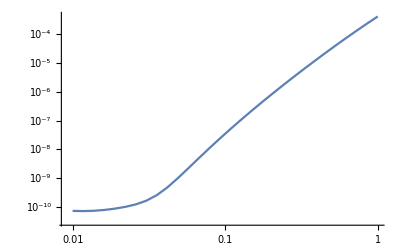

```mathematica
data=Transpose@{times,1-fid};
ListLogLogPlot[data,Joined->True]
```

```mathematica
Re[Log10[1-fid[[1]]]]
```

-10.1359